Settings + functions.

```mathematica
Unprotect[Internal`EncodeCharacters];

Internal`EncodeCharacters[str_,enc_]:=Quiet[FromCharacterCode[ToCharacterCode[str],enc]]

SetDirectory[NotebookDirectory[]]
```

D:\Документы\Diploma Mag\Noises_Nb

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogLinearPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier",FontSize->12, Bold},ImageSize->500,PlotStyle->{Red,PointSize[0.005]}];
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, -1}],{1,Round[Length[x]/2]+1}]]
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
FreqList[x_]:=Table[1.0*b/Length[x],{b,0,Length[x]-1}]
Freq[x_]:=FreqList[x][[NumPlace[x]]]
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[NumPlace[x]-1;;NumPlace[x]+1]],AbsFourier[x][[NumPlace[x]-1;;NumPlace[x]+1]]}],FrameLabel->{"ν","A, mm"}]
FullPlot[x_]:=ListLinePlot[Transpose[{FreqList[x][[1;;Round[Length[x]/2]+1]],AbsFourier[x]}],FrameLabel->{"ν","A, mm"}]
FreqList2[x_]:=Table[1.0*b/Length[Total[Transpose[x]]],{b,0,Length[Total[Transpose[x]]]-1}]
FullPlot2[x_]:=ListLinePlot[Transpose[{FreqList2[Total[Transpose[x]]][[1;;Round[Length[Total[Transpose[x]]]/2]+1]],Total[Transpose[x]]}],FrameLabel->{"ν","A, mm"}]
```

First steps.

```mathematica
dirs=FileNames["data_with_noise_for_denisov — 2"]
```

{data_with_noise_for_denisov — 2}

```mathematica
files=FileNames["v2k_bpm_xy_1*",dirs]
```

{data_with_noise_for_denisov — 2\v2k_bpm_xy_1-000.sdds,data_with_noise_for_denisov — 2\v2k_bpm_xy_1-001.sdds,data_with_noise_for_denisov — 2\v2k_bpm_xy_1-002.sdds,data_with_noise_for_denisov — 2\v2k_bpm_xy_1-003.sdds,data_with_noise_for_denisov — 2\v2k_bpm_xy_1-004.sdds,data_with_noise_for_denisov — 2\v2k_bpm_xy_1-005.sdds}

```mathematica
datas=Take[Transpose@Import[#,"Table",HeaderLines->13],{3,4}]&/@files;
```

```mathematica
sum =Total[datas];
```

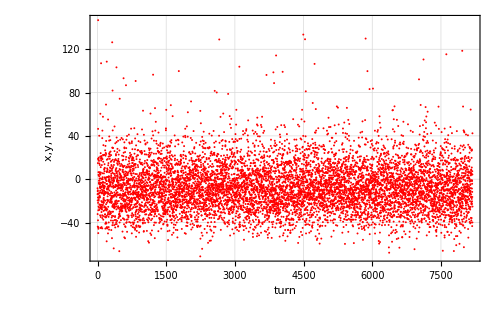

```mathematica
ListPlot[sum[[1]],PlotStyle->{Red},FrameLabel->{"turn","x,y, mm"}]
```

Real work.

```mathematica
dirs=FileNames["data_with_noise_for_denisov"]
```

{data_with_noise_for_denisov}

```mathematica
first=FileNames["v2k_bpm_xy_1*",dirs];
```

```mathematica
FirstdataX=Flatten@Take[Transpose@Import[#,"Table",HeaderLines->13],{3}]&/@first;
```

False

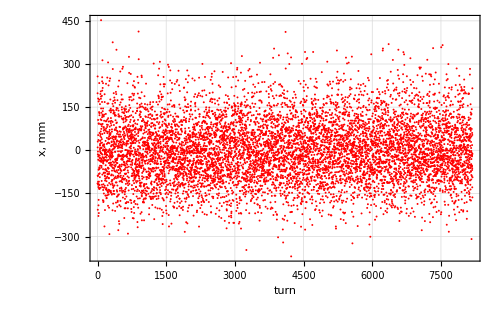

```mathematica
NoiseFirstX =Total[FirstdataX];
NoiseFirstX = NoiseFirstX - Mean[NoiseFirstX];
NoiseFirstX//MatrixQ
ListPlot[NoiseFirstX,PlotStyle->{Red},FrameLabel->{"turn","x, mm"}]
```

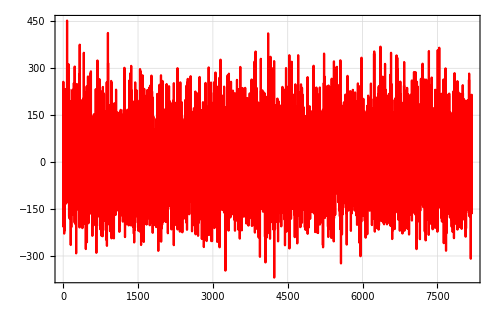

```mathematica
Image1X=ListLinePlot[NoiseFirstX]
```

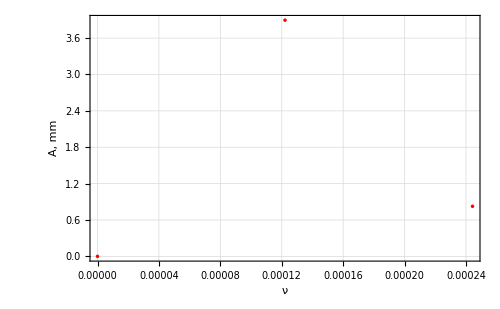

```mathematica
Fourier1X=TruePlot[NoiseFirstX]
```

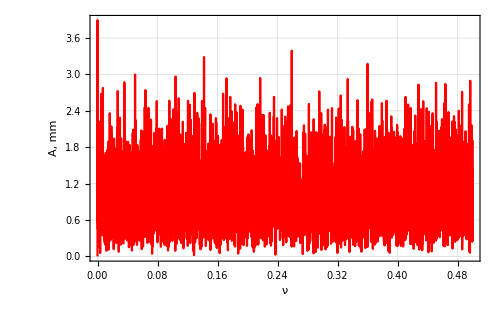

```mathematica
FourierFull1X=FullPlot[NoiseFirstX]
```

```mathematica
FirstdataY=Flatten@Take[Transpose@Import[#,"Table",HeaderLines->13],{4}]&/@first;
```

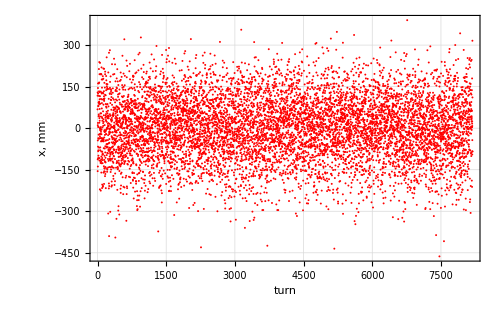

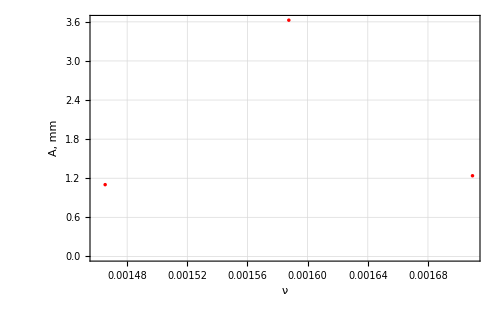

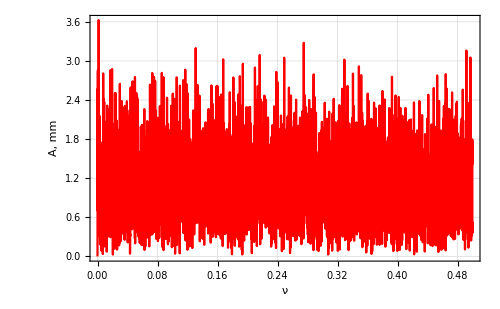

```mathematica
NoiseFirstY =Total[FirstdataY];
NoiseFirstY = NoiseFirstY - Mean[NoiseFirstY];
ListPlot[NoiseFirstY,PlotStyle->{Red},FrameLabel->{"turn","x, mm"}]
Fourier1Y=TruePlot[NoiseFirstY]
FourierFull1Y=FullPlot[NoiseFirstY]
```

```mathematica
second=FileNames["v2k_bpm_xy_2*",dirs];
```

```mathematica
SeconddataX=Flatten@Take[Transpose@Import[#,"Table",HeaderLines->13],{3}]&/@second;
SeconddataY=Flatten@Take[Transpose@Import[#,"Table",HeaderLines->13],{4}]&/@second;
```

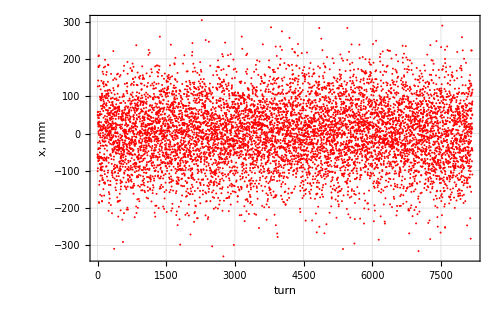

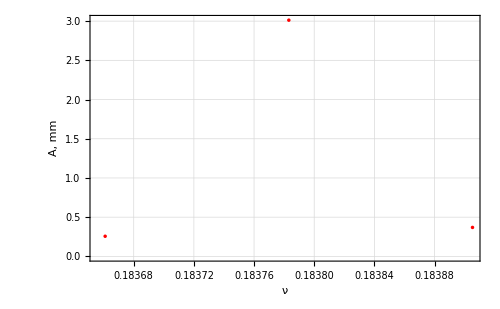

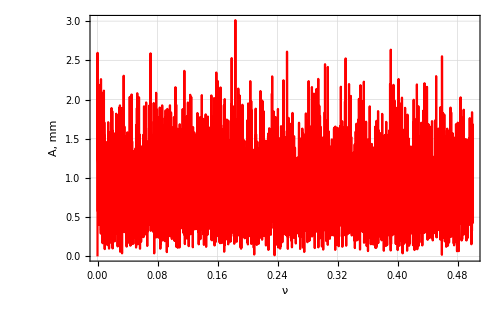

```mathematica
Noise2X =Total[SeconddataX];
Noise2X = Noise2X - Mean[Noise2X];
ListPlot[Noise2X,PlotStyle->{Red},FrameLabel->{"turn","x, mm"}]
Fourier2X=TruePlot[Noise2X]
FourierFull2X=FullPlot[Noise2X]
```

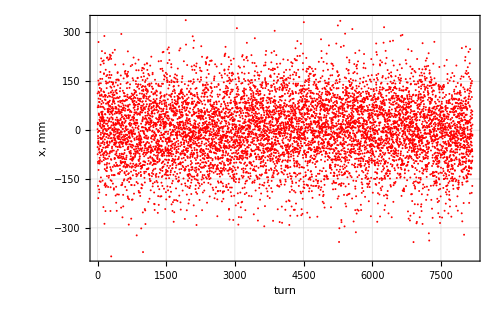

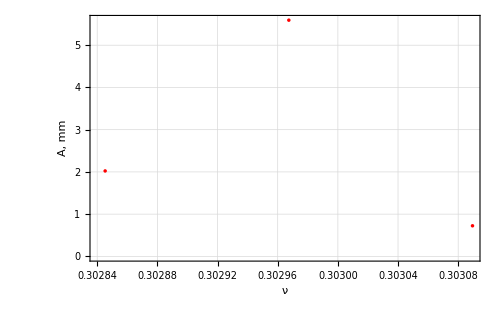

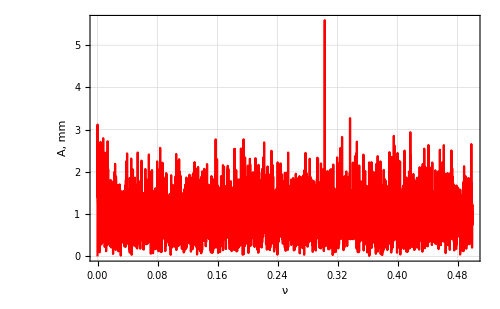

```mathematica
Noise2Y =Total[SeconddataY];
Noise2Y = Noise2Y - Mean[Noise2Y];
ListPlot[Noise2Y,PlotStyle->{Red},FrameLabel->{"turn","x, mm"}]
Fourier2Y=TruePlot[Noise2Y]
FourierFull2Y=FullPlot[Noise2Y]
```

```mathematica
third=FileNames["v2k_bpm_xy_3*",dirs];
```

```mathematica
ThirddataX=Flatten@Take[Transpose@Import[#,"Table",HeaderLines->13],{3}]&/@third;
ThirddataY=Flatten@Take[Transpose@Import[#,"Table",HeaderLines->13],{4}]&/@third;
```

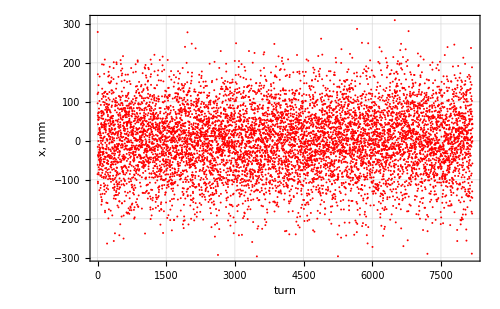

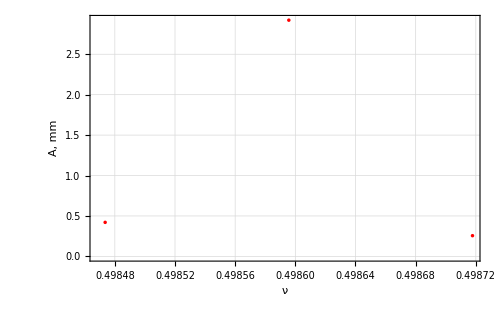

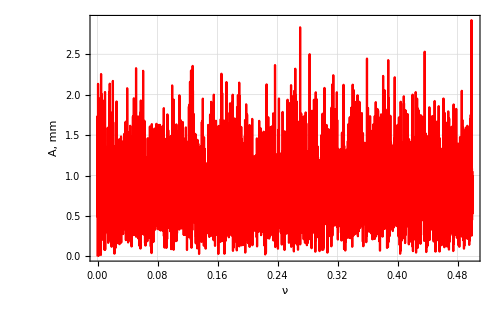

```mathematica
Noise3X =Total[ThirddataX];
Noise3X = Noise3X - Mean[Noise3X];
ListPlot[Noise3X,PlotStyle->{Red},FrameLabel->{"turn","x, mm"}]
Fourier3X=TruePlot[Noise3X]
FourierFull3X=FullPlot[Noise3X]
```

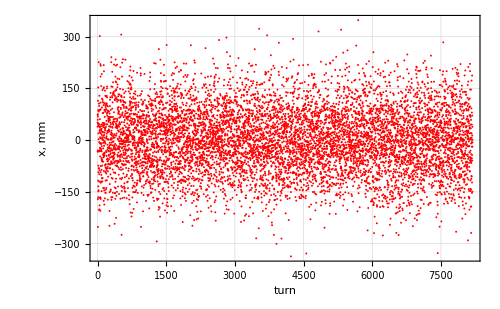

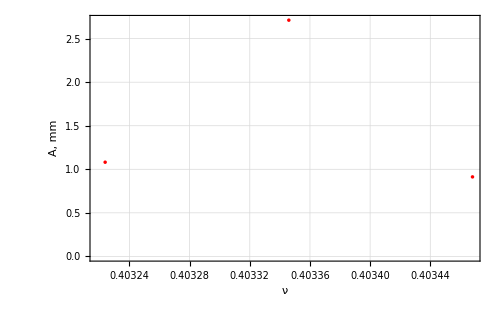

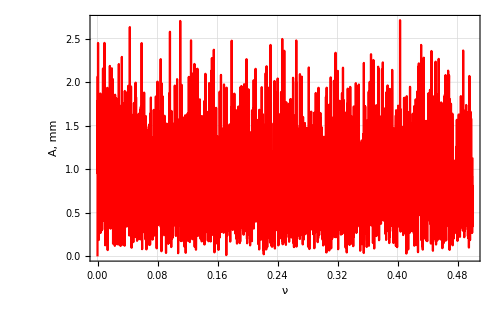

```mathematica
Noise3Y =Total[ThirddataY];
Noise3Y = Noise3Y - Mean[Noise3Y];
ListPlot[Noise3Y,PlotStyle->{Red},FrameLabel->{"turn","x, mm"}]
Fourier3Y=TruePlot[Noise3Y]
FourierFull3Y=FullPlot[Noise3Y]
```

```mathematica
fourth=FileNames["v2k_bpm_xy_4*",dirs]
(*fourth =Take[fourth,4]*)
```

{data_with_noise_for_denisov\v2k_bpm_xy_4-000.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-001.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-002.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-003.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-004.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-005.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-006.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-007.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-008.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-009.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-010.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-011.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-012.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-013.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-014.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-015.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-016.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-017.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-018.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-019.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-020.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-021.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-022.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-023.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-024.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-025.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-026.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-027.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-028.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-029.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-030.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-031.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-032.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-033.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-034.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-035.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-036.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-037.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-038.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-039.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-040.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-041.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-042.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-043.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-044.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-045.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-046.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-047.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-048.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-049.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-050.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-051.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-052.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-053.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-054.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-055.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-056.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-057.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-058.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-059.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-060.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-061.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-062.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-063.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-064.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-065.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-066.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-067.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-068.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-069.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-070.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-071.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-072.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-073.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-074.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-075.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-076.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-077.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-078.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-079.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-080.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-081.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-082.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-083.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-084.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-085.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-086.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-087.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-088.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-089.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-090.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-091.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-092.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-093.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-094.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-095.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-096.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-097.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-098.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-099.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-100.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-101.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-102.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-103.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-104.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-105.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-106.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-107.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-108.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-109.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-110.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-111.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-112.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-113.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-114.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-115.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-116.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-117.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-118.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-119.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-120.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-121.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-122.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-123.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-124.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-125.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-126.sdds,data_with_noise_for_denisov\v2k_bpm_xy_4-127.sdds}

```mathematica
FourthdataX=Flatten@Take[Transpose@Import[#,"Table",HeaderLines->13],{3}]&/@fourth;
FourthdataY=Flatten@Take[Transpose@Import[#,"Table",HeaderLines->13],{4}]&/@fourth;
```

```mathematica
Dimensions@FourthdataX
```

{128,8189}

```mathematica
(*ListPlot/@FourthdataX*)
```

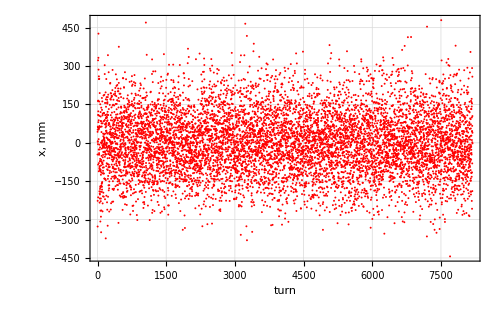

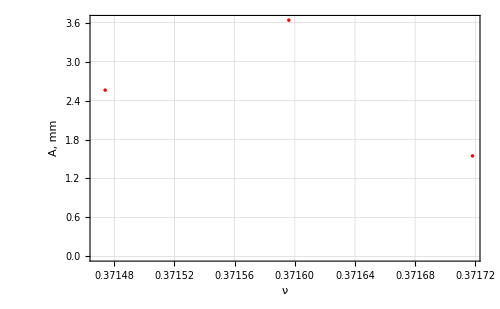

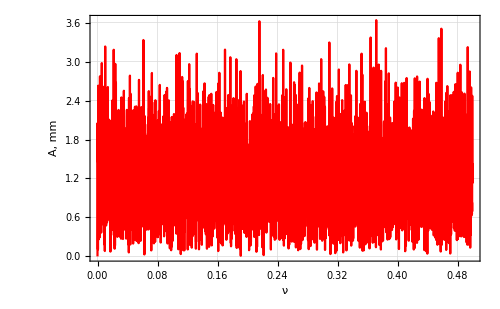

```mathematica
Noise4X =Total[FourthdataX];
Noise4X = Noise4X - Mean[Noise4X];
ListPlot[Noise4X,PlotStyle->{Red},FrameLabel->{"turn","x, mm"}]
Fourier4X=TruePlot[Noise4X]
FourierFull4X=FullPlot[Noise4X]
```

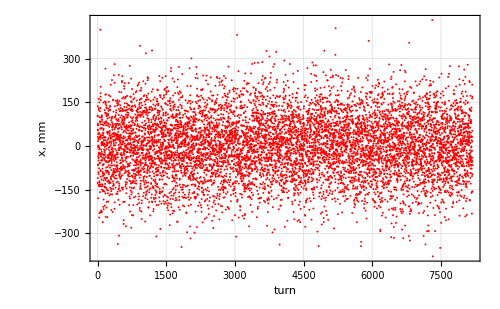

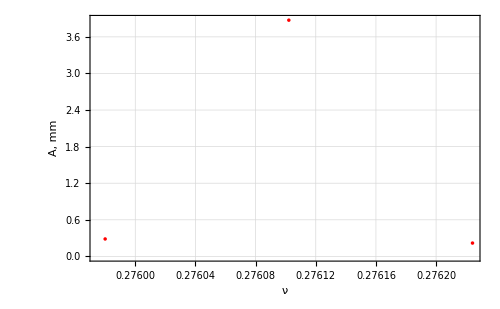

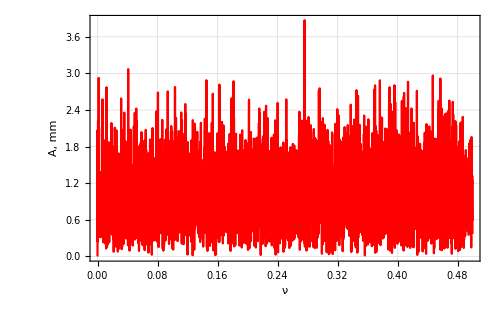

```mathematica
Noise4Y =Total[FourthdataY];
Noise4Y = Noise4Y - Mean[Noise4Y];
ListPlot[Noise4Y,PlotStyle->{Red},FrameLabel->{"turn","x, mm"}]
Fourier4Y=TruePlot[Noise4Y]
FourierFull4Y=FullPlot[Noise4Y]
```

Метод Ю.А.Роговского

```mathematica
data4X=(#)&/@FourthdataX;
dataM4X=(#-Mean[#])&/@data4X;
```

```mathematica
Dimensions@data4X
```

{128,8189}

```mathematica
f4X=Abs@Fourier[#]&/@dataM4X;
```

```mathematica
Dimensions@f4X
```

{128,8189}

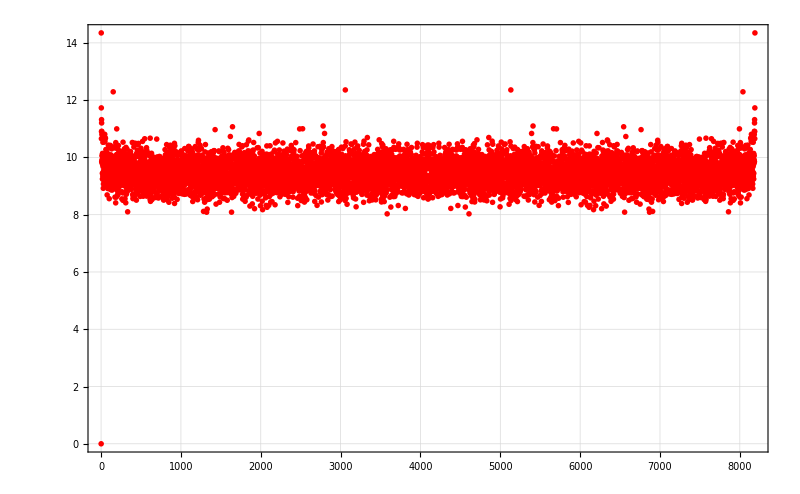

```mathematica
ListPlot[(Total/@(Chop@Transpose[f4X])/Length[f4X]),ImageSize->800]
```

```mathematica
data4Y=(#)&/@FourthdataY;
dataM4Y=(#-Mean[#])&/@data4Y;
```

```mathematica
Dimensions[data4Y]
```

{128,8189}

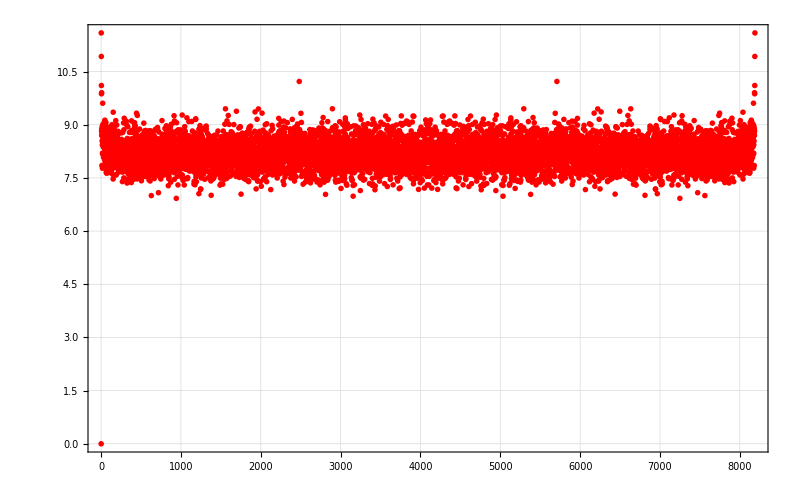

```mathematica
f4Y=Abs@Fourier[#]&/@dataM4Y;
ListPlot[(Total/@(Chop@Transpose[f4Y])/Length[f4Y]),ImageSize->800]
```

{128,4095}

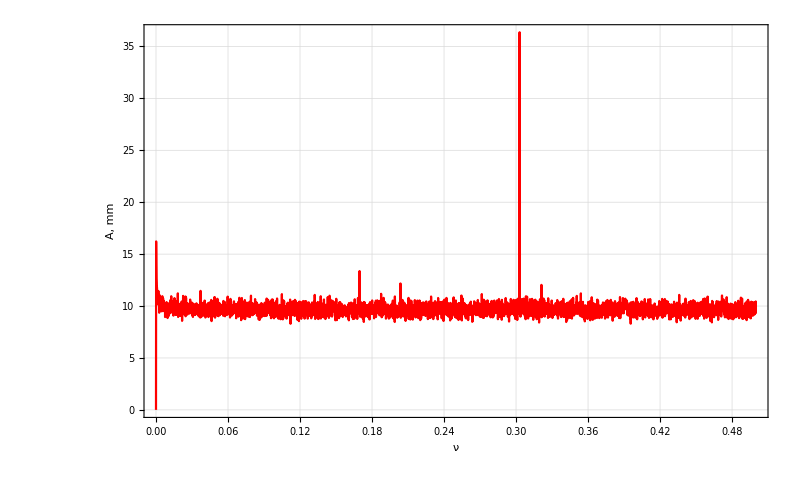

```mathematica
data2X=(#)&/@SeconddataX;
dataM2X=(#-Mean[#])&/@data2X;
f2X = AbsFourier[#]&/@dataM2X;
Dimensions[f2X]
tf2X = Total[f2X];
FreqList2X=Table[1.0*b/Length[data2X[[1]]],{b,0,Length[data2X[[1]]]-1}];
FullPlot2X =ListLinePlot[Transpose[{FreqList2X[[1;;Round[Length[data2X[[1]]]/2]+1]],tf2X}],FrameLabel->{"ν","A, mm"},ImageSize->800]
(*Fourierf1X=FullPlot2[f1X]*)
```

{128,4095}

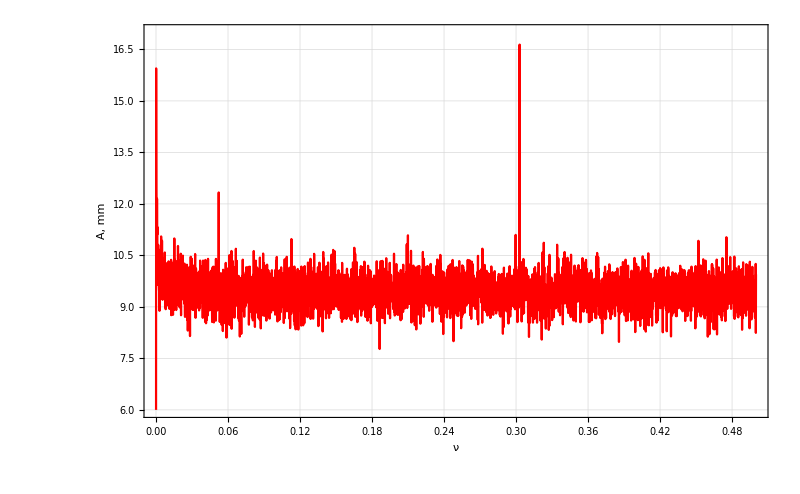

```mathematica
data3X=(#)&/@ThirddataX;
dataM3X=(#-Mean[#])&/@data3X;
f3X = AbsFourier[#]&/@dataM3X;
Dimensions[f3X]
tf3X = Total[f3X];
FreqList3X=Table[1.0*b/Length[data3X[[1]]],{b,0,Length[data3X[[1]]]-1}];
FullPlot3X =ListLinePlot[Transpose[{FreqList3X[[1;;Round[Length[data3X[[1]]]/2]+1]],tf3X}],FrameLabel->{"ν","A, mm"},ImageSize->800, PlotRange->{6,17}]
```

{128,4095}

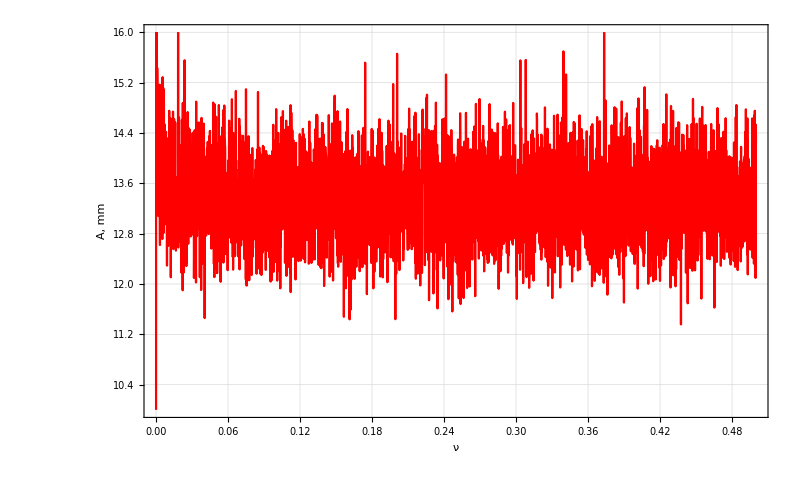

```mathematica
data4X=(#)&/@FourthdataX;
dataM4X=(#-Mean[#])&/@data4X;
f4X = AbsFourier[#]&/@dataM4X;
Dimensions[f4X]
tf4X = Total[f4X];
FreqList4X=Table[1.0*b/Length[data4X[[1]]],{b,0,Length[data4X[[1]]]-1}];
FullPlot4X =ListLinePlot[Transpose[{FreqList4X[[1;;Round[Length[data4X[[1]]]/2]+1]],tf4X}],FrameLabel->{"ν","A, mm"},ImageSize->800, PlotRange->{10,16}]
```

{128,4095}

{4095}

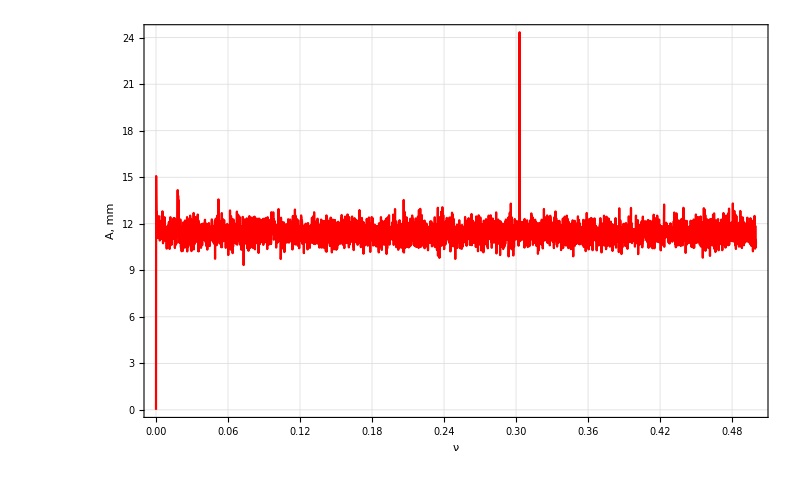

```mathematica
data1X=(#)&/@FirstdataX;
dataM1X=(#-Mean[#])&/@data1X;
f1X = AbsFourier[#]&/@dataM1X;
Dimensions[f1X]
tf1X = Total[f1X];
Dimensions[tf1X]
FreqList1X=Table[1.0*b/Length[data1X[[1]]],{b,0,Length[data1X[[1]]]-1}];
FullPlot1X =ListLinePlot[Transpose[{FreqList1X[[1;;Round[Length[data1X[[1]]]/2]+1]],tf1X}],FrameLabel->{"ν","A, mm"},ImageSize->800]
```

```mathematica
SuperPlot[{fileName_,xyData_}]:=Module[{file,data,p1,p2,p3,p4,datta,dattta,ret,len, AF1, AF,FL, FRQ,NP},
dattta=Mean[xyData];
datta =(#-dattta)&/@xyData;
len=Length@First@xyData;

Print[dattta];
AF1= AbsFourier[#]&/@datta;
(*AF = Total[AF1];
NP = Position[AF,Max[AF]][[1,1]];FL =Take[ Table[1.0*b/len,{b,0,len-1}],{1,Round[len/2]+1}];FRQ  = FL[[NP]];
(*AF = Transpose@{FreqList,#}&/@AbsFourier*);p4 = ListPlot[Transpose[{FL[[NP-1;;NP+1]],AF[[NP-1;;NP+1]]}],FrameLabel->{"ν","A, mm"}];p3 = ListLinePlot[Transpose[{FL,AF}],FrameLabel->{"ν","A, mm"}, PlotLabel->FRQ];
*)
p1=ListPlot[xyData,PlotStyle->{Red,Blue},FrameLabel->{"turn","x,y, mm"}, PlotLabel->"Signal"];
(*p2=ListPlot[Transpose@xyData,PlotStyle->Black,FrameLabel->{"x, mm","y, mm"}, PlotLabel->"Beam"]*);
(*p3=ListPlot[AbsFourier,PlotStyle->{Red,Blue},FrameLabel->{"ν","A, mm"}, PlotLabel->Freq]*);

ret={p1,p2,p3,p4};
Return[p1];
];
```

```mathematica
files=FileNames["v2k_bpm_xy_1*",dirs];
datas=Flatten@Take[Transpose@Import[#,"Table",HeaderLines->13],{3}]&/@files;
(*SuperPlot[#]&/@Transpose[{files,datas}]*)
```

-1.08323

Fourier::fftl: Argument 6.90628 is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument -5.71621 is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier::fftl will be suppressed during this calculation.

-1.2534

-1.86214

-0.944741

-0.592729

-1.38059

-1.47604

-0.981155

-0.765715

-1.04887

-0.98262

-1.09268

-1.30887

-1.33925

-1.95906

-0.754381

-1.43016

-1.77672

-1.63427

-1.06548

-1.48499

-0.448736

-1.13617

-1.19713

-1.06576

-0.788766

-0.549221

-1.22008

-1.43528

-0.795712

-1.16385

-1.07697

-1.68739

-1.44154

-1.6236

-1.94012

-1.8202

-0.523293

-1.15129

-1.19134

-1.16869

-1.40441

-1.53227

-1.3174

-0.614181

-0.846454

-0.991995

-1.04029

-0.907692

-1.10701

-1.14044

-1.31519

-2.01844

-1.66161

-1.74695

-1.38637

-1.28712

-1.70434

-1.57557

-1.78134

-1.74806

-1.15098

-2.30706

-2.01378

-1.92897

-2.09429

-1.66374

-1.82282

-2.00971

-2.06898

-1.54345

-0.837425

-1.66106

-1.34625

-2.10002

-1.23268

-1.33918

-0.573088

-0.726703

-1.80445

-1.15025

-1.69185

-1.72031

-1.72482

-1.27073

-1.92029

-2.29205

-2.28459

-1.44333

-1.77314

-1.50163

-1.50527

-1.22026

-1.63734

-1.55221

-1.49305

-1.73321

-2.08913

-1.59078

-1.45551

-1.79014

-1.8751

-1.95915

-1.97849

-1.15364

-1.63895

-1.11147

-0.983911

-1.46616

-2.10329

-0.920539

-1.41088

-1.82009

-1.67667

-1.94711

-1.35755

-1.13864

-1.55665

-1.62313

-1.03581

-1.28823

-0.451493

-1.17464

-1.04781

-2.03687

-1.81326

-0.936235

-1.24106

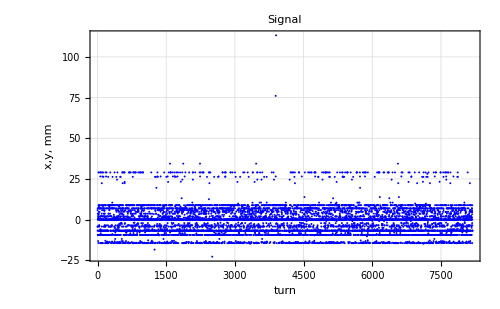
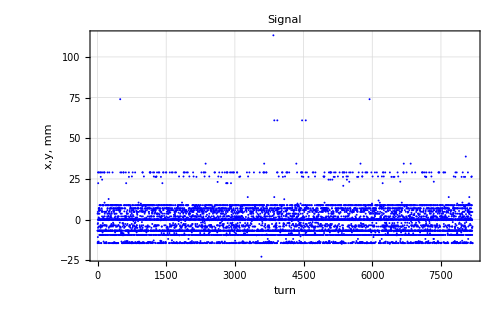
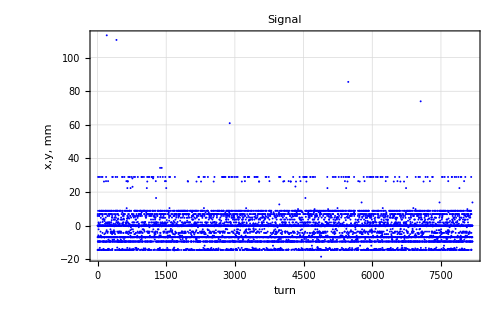
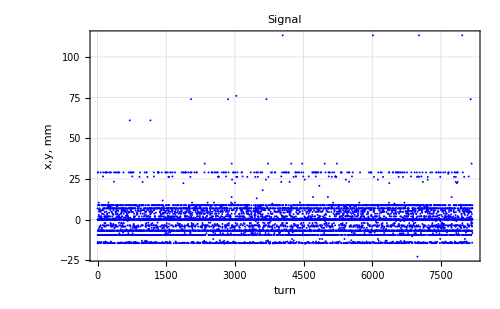
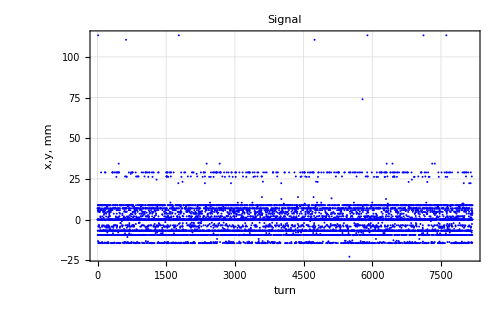
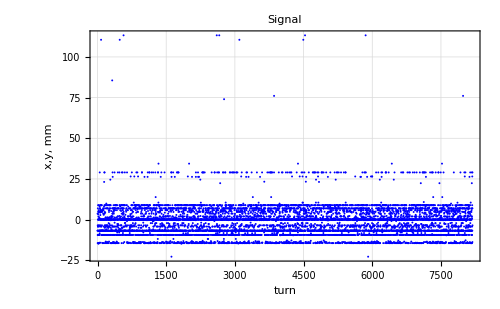
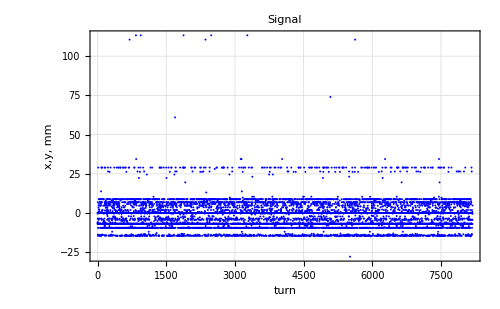
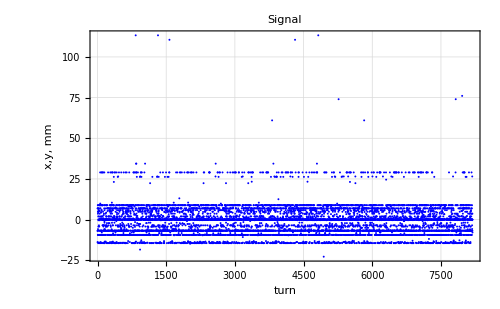
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*abcd =AbsFourier[#]&/@datas;
abcde = Total[abcd];*)
(*Dimensions[abcde]
Dimensions[FLas]
Dimensions[datas]*)
SuperPlot[#]&/@Transpose[{files, datas}]
```